## Modifying Lists

In this lecture, we’ll look at functions that modify and transform lists.

### Adding Elements

Let’s start by looking at how to add elements to lists.

First, let’s create a list which we can use to demonstrate the functions. We’ll use the Alphabet function to create a list of all the characters in the alphabet:

```mathematica
alpha=Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

To add an element to the end of a list:

```mathematica
Append[alpha,"Last Element"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

Note that lists in Mathematica are immutable. When you append, you create a new list. Notice that the original list is the same:

```mathematica
alpha
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

If you wanted myList to contain “Last Element”, you should set myList to the result:

```mathematica
alpha=Append[alpha,"Last Element"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

To add an element at the beginning of a list:

```mathematica
alpha=Prepend[alpha,"First Element"]
```

{First Element,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

To insert an element in a list:

```mathematica
alpha=Insert[alpha,"4th Element",4]
```

{First Element,a,b,4th Element,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

### Removing Elements

To delete specific elements in a list, use Delete:

```mathematica
?Delete
```

RowBox[{"Delete", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] deletes the element at position StyleBox["n", "TI"] in StyleBox["expr", "TI"]. If StyleBox["n", "TI"] is negative, the position is counted from the end. 
RowBox[{"Delete", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] deletes the part at position RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]. 
RowBox[{"Delete", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] deletes parts at several positions. 
RowBox[{"Delete", "[", StyleBox["pos", "TI"], "]"}] represents an operator form of Delete that can be applied to an expression.

```mathematica
Delete[alpha,1]
```

{a,b,4th Element,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

To delete all the elements we just added, we use the 3rd form of Delete:

```mathematica
alpha=Delete[alpha,{{1},{4},{-1}}]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

To delete ranges of elements in a list, use Drop:

```mathematica
?Drop
```

RowBox[{"Drop", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives StyleBox["list", "TI"] with its first StyleBox["n", "TI"] elements dropped. 
RowBox[{"Drop", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"-", StyleBox["n", "TI"]}]}], "]"}] gives StyleBox["list", "TI"] with its last StyleBox["n", "TI"] elements dropped. 
RowBox[{"Drop", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", StyleBox["n", "TI"], "}"}]}], "]"}] gives StyleBox["list", "TI"] with its StyleBox["n", "TI"]SuperscriptBox["", "th"] element dropped. 
RowBox[{"Drop", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["n", "TI"]}], "}"}]}], "]"}] gives StyleBox["list", "TI"] with elements StyleBox["m", "TI"] through StyleBox["n", "TI"] dropped. 
RowBox[{"Drop", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["s", "TI"]}], "}"}]}], "]"}] gives StyleBox["list", "TI"] with elements StyleBox["m", "TI"] through StyleBox["n", "TI"] in steps of StyleBox["s", "TI"] dropped. 
RowBox[{"Drop", "[", RowBox[{StyleBox["list", "TI"], ",", SubscriptBox[StyleBox["seq", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["seq", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives a nested list in which elements specified by SubscriptBox[StyleBox["seq", "TI"], StyleBox["i", "TI"]] have been dropped at level StyleBox["i", "TI"] in StyleBox["list", "TI"].

```mathematica
nums=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Drop[nums,5]
```

{6,7,8,9,10}

```mathematica
Drop[nums,-5]
```

{1,2,3,4,5}

```mathematica
Drop[nums,{2,4}]
```

{1,5,6,7,8,9,10}

Every other element:

```mathematica
Drop[nums,{1,Length[nums],2}]
```

{2,4,6,8,10}

We can also use -1 to represent the last element:

```mathematica
Drop[nums,{1,-1,2}]
```

{2,4,6,8,10}

### Join, Gather and Tally

Let’s generate 3 ranges which we can use to demonstrate the Join, Gather and Tally functions:

```mathematica
range1 = Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
range2=Range[15,7,-1]
```

{15,14,13,12,11,10,9,8,7}

```mathematica
range3=Range[4,12]
```

{4,5,6,7,8,9,10,11,12}

We join the lists together with the Join function:

```mathematica
?Join
```

RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] concatenates lists or other expressions that share the same head.
RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", StyleBox["n", "TI"]}], "]"}] joins the objects at level StyleBox["n", "TI"] in each of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]].

Let's join the lists together :

```mathematica
joined = Join[range1,range2,range3]
```

{1,2,3,4,5,6,7,8,9,10,15,14,13,12,11,10,9,8,7,4,5,6,7,8,9,10,11,12}

We can visualize this list with ListPlot:

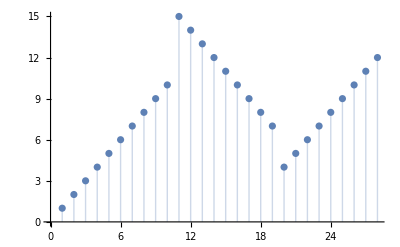

```mathematica
ListPlot[joined,Filling->Axis]
```

We can remove duplicate entries from the list with DeleteDuplicates:

```mathematica
DeleteDuplicates[joined]
```

{1,2,3,4,5,6,7,8,9,10,15,14,13,12,11}

If instead of deleting the duplicates we want to gather the duplicates together, we use the Gather function:

```mathematica
?Gather
```

RowBox[{"Gather", "[", StyleBox["list", "TI"], "]"}] gathers the elements of StyleBox["list", "TI"] into sublists of identical elements.
RowBox[{"Gather", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["test", "TI"]}], "]"}] applies StyleBox["test", "TI"] to pairs of elements to determine if they should be considered identical.

We can apply Gather to our joined list:

```mathematica
Gather[joined]
```

{{1},{2},{3},{4,4},{5,5},{6,6},{7,7,7},{8,8,8},{9,9,9},{10,10,10},{15},{14},{13},{12,12},{11,11}}

We can count the number of times an element occurs with Tally:

```mathematica
?Tally
```

RowBox[{"Tally", "[", StyleBox["list", "TI"], "]"}] tallies the elements in StyleBox["list", "TI"], listing all distinct elements together with their multiplicities.
RowBox[{"Tally", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["test", "TI"]}], "]"}] uses StyleBox["test", "TI"] to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

The Tally of our list is:

```mathematica
tallied=Tally[joined]
```

{{1,1},{2,1},{3,1},{4,2},{5,2},{6,2},{7,3},{8,3},{9,3},{10,3},{15,1},{14,1},{13,1},{12,2},{11,2}}

### Other Useful Operations

In this section, we’ll look at some other useful functions that operate on lists.

RotateLeft moves elements from the left of the list to the right:

```mathematica
?RotateLeft
```

RowBox[{"RotateLeft", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] cycles the elements in StyleBox["expr", "TI"] StyleBox["n", "TI"] positions to the left. 
RowBox[{"RotateLeft", "[", StyleBox["expr", "TI"], "]"}] cycles one position to the left. 
RowBox[{"RotateLeft", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] cycles elements at successive levels SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] positions to the left.

```mathematica
range1
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
RotateLeft[range1]
```

{2,3,4,5,6,7,8,9,10,1}

```mathematica
RotateLeft[range1,3]
```

{4,5,6,7,8,9,10,1,2,3}

RotateRight moves elements from the right of the list to the left:

```mathematica
?RotateRight
```

RowBox[{"RotateRight", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] cycles the elements in StyleBox["expr", "TI"] StyleBox["n", "TI"] positions to the right. 
RowBox[{"RotateRight", "[", StyleBox["expr", "TI"], "]"}] cycles one position to the right. 
RowBox[{"RotateRight", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] cycles elements at successive levels SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] positions to the right.

```mathematica
RotateRight[range1,3]
```

{8,9,10,1,2,3,4,5,6,7}

This is the same as rotating left by -3:

```mathematica
RotateLeft[range1,-3]
```

{8,9,10,1,2,3,4,5,6,7}

Sometimes, you need two lists to be the same length. For instance, suppose that you had u and v:

```mathematica
u=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
v=Range[5]
```

{1,2,3,4,5}

You can’t add u to v:

```mathematica
u+v
```

Thread::tdlen: Objects of unequal length in {1,2,3,4,5,6,7,8,9,10}+{1,2,3,4,5} cannot be combined.

{1,2,3,4,5}+{1,2,3,4,5,6,7,8,9,10}

If you knew you wanted to add u to the first 5 elements, then you could pad u on the right with zeroes:

```mathematica
?PadRight
```

RowBox[{"PadRight", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] makes a list of length StyleBox["n", "TI"] by padding StyleBox["list", "TI"] with zeros on the right. 
RowBox[{"PadRight", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["x", "TI"]}], "]"}] pads by repeating the element StyleBox["x", "TI"]. 
RowBox[{"PadRight", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] pads by cyclically repeating the elements SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"PadRight", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["m", "TI"]}], "]"}] leaves a margin of StyleBox["m", "TI"] elements of padding on the left. 
RowBox[{"PadRight", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] makes a nested list with length SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] at level StyleBox["i", "TI"]. 
RowBox[{"PadRight", "[", StyleBox["list", "TI"], "]"}] pads a ragged array StyleBox["list", "TI"] with zeros to make it full.

```mathematica
PadRight[v,Length[u]]
```

{1,2,3,4,5,0,0,0,0,0}

Then add them together:

```mathematica
u+PadRight[v,Length[u]]
```

{2,4,6,8,10,6,7,8,9,10}

You can also use PadLeft:

```mathematica
?PadLeft
```

RowBox[{"PadLeft", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] makes a list of length StyleBox["n", "TI"] by padding StyleBox["list", "TI"] with zeros on the left. 
RowBox[{"PadLeft", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["x", "TI"]}], "]"}] pads by repeating the element StyleBox["x", "TI"]. 
RowBox[{"PadLeft", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] pads by cyclically repeating the elements SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"PadLeft", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["m", "TI"]}], "]"}] leaves a margin of StyleBox["m", "TI"] elements of padding on the right. 
RowBox[{"PadLeft", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] makes a nested list with length SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] at level StyleBox["i", "TI"]. 
RowBox[{"PadLeft", "[", StyleBox["list", "TI"], "]"}] pads a ragged array StyleBox["list", "TI"] with zeros to make it full.

```mathematica
PadLeft[v,10]
```

{0,0,0,0,0,1,2,3,4,5}

Note that this is the same as PadRight with a negative length:

```mathematica
PadRight[v,-10]
```

{0,0,0,0,0,1,2,3,4,5}

### Summary

This lecture, focused primarily on functions that modify Lists. We looked at inserting and removing elements from lists, joining lists and tallying their elements as well some other useful functions. In the next lecture, we’ll look at search and sorting lists, set operations on lists and some basic combinatorics.